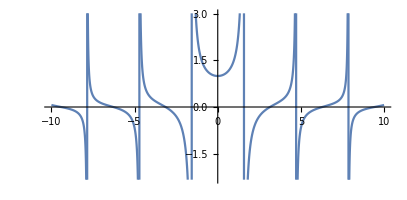

```mathematica
f1[x_]:=Expand[(Tan[x])/x]
Plot[f1[x],{x,-10,10}, AspectRatio->Automatic]  (*El dominio de la función f1 son todos los reales menos  x=0, y x=(n*pi)/2 siendo n un entero impar*)
```

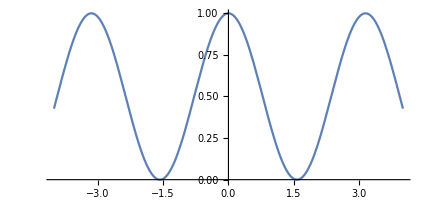
```mathematica
f2[x_]:=Expand[(Cos[x])^2] (*el dominio va de -infinito a +infinito y el rango es [0,1]*)
Plot[f2[x],{x,-4,4},AspectRatio->Automatic]
-Graphics-
```

```mathematica
f3[x_]:=Expand[(Sin[x])^2]   (*el dominio va de -INF a +INF y el rango es [0,1]*)
Plot[f3[x],{x,-4,4},AspectRatio->Automatic]
```

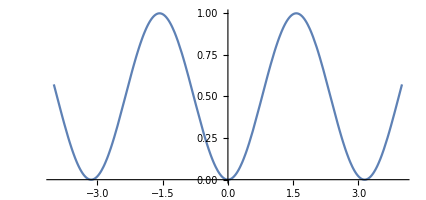
```mathematica
-Graphics-


(*Voy a graficar f2+f3, es decir (Cos(x)^2)+(Sen(x)^2) lo cual debería ser igual a 1 segun la identidad trigonometrica*)
```

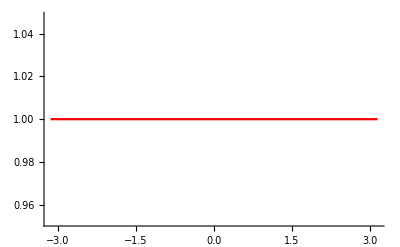

```mathematica
Plot[{f2[x]+f3[x]},{x,-Pi,Pi}, PlotStyle->Red]
```

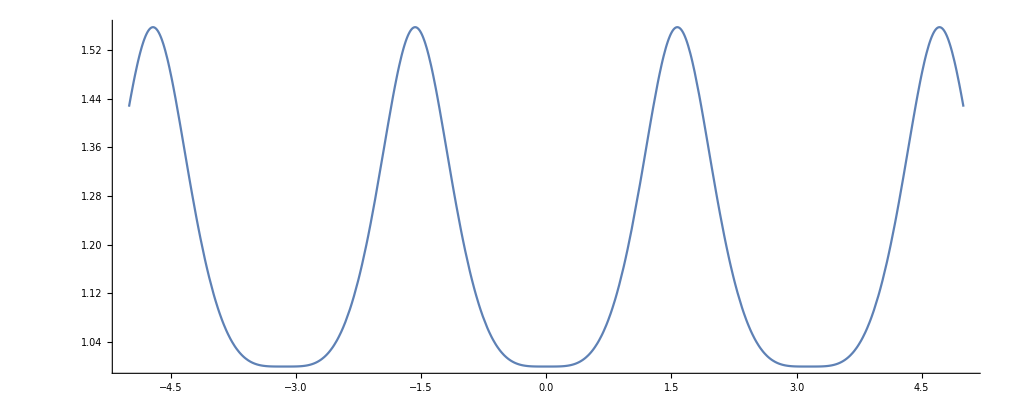

```mathematica
(*El dominio son todos los reales y la imagen es =1, es una funcion continua... *)




(*Ahora voy a graficar a la función f1 evaluada en f3, es decir f1(f3(x))*)
Plot[f1[f3[x]],{x,-5,5}, AspectRatio->Automatic]
```

```mathematica
(*El dominio no puede ser todos los reales aunque parezca que así es, por ejemplo para x=pi o x=2pi el Sen se hace 0 y me queda un hueco en la función ya que no está definida para ese punto*)
```